```mathematica
Needs["HierarchicalClustering`"]
SetOptions[MatrixPlot,ImageSize->200{1,1}];
```

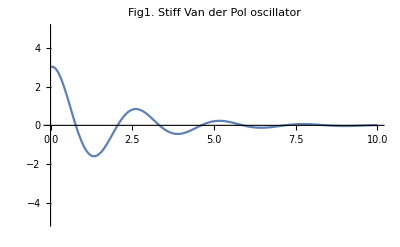

```mathematica
Module[{tmax=10.,δ=1,k=N[2π],T1=0.1,Am=0.},
vdp=NDSolveValue[{x''[t]+δ x'[t]+k x[t]==Am Sin[2 π t/T1],x[0]==3,x'[0]==1},x,{t,0,tmax},Method->"ExplicitRungeKutta"];
Plot[vdp[t],{t,0.,tmax},PlotLabel->"Fig1. Damped oscillator (linear pendulum or spring mass damper system)",PlotRange->{{0,tmax},{-5,5}}]
]
```

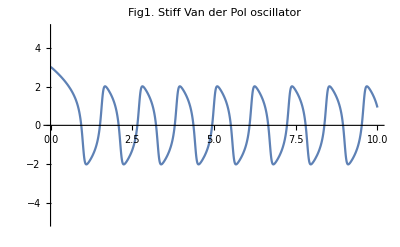
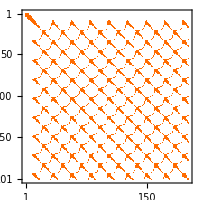

```mathematica
Module[{tmax=10.,μ=10,k=N[2π],T1=0.1,Am=0.},
vdp=NDSolveValue[{x''[t]+μ(x[t]^2-1)x'[t]+k^2 x[t]==Am Sin[2 π t/T1],x[0]==3,x'[0]==1},x,{t,0,tmax}];
Plot[vdp[t],{t,0.,tmax},PlotLabel->"Fig1. Stiff Van der Pol oscillator",PlotRange->{{0,tmax},{-5,5}}]
With[{stepSize=0.05,end=tmax},MatrixPlot[UnitStep[0.1-DistanceMatrix[vdp[Range[0,end,stepSize]]]]]]

]
```

ParametricFunction[<>]

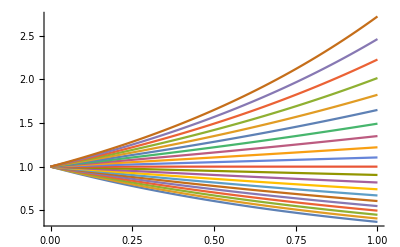

```mathematica
pfun=ParametricNDSolveValue[{y'[t]==a y[t],y[0]==1},y,{t,0,10},{a}]
Plot[Evaluate[Table[pfun[a][t],{a,-1,1,.1}]],{t,0,1},PlotRange->All]
```

ParametricFunction[<>]

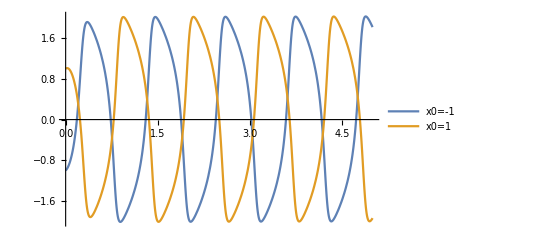

```mathematica
Am=50.;k=N[2π];tmax=5;T1=1000;μ=10;
pfun=ParametricNDSolveValue[{x''[t]+μ(x[t]^2-1)x'[t]+k^2 x[t]==Am Sin[2 π t/T1],x[0]==x0,x'[0]==1},x,{t,0,tmax},{x0}]

Plot[Evaluate[Table[pfun[x0][t],{x0,-1,1,2}]],{t,0,tmax},PlotRange->All,PlotLegends->{"x0=-1","x0=1"}]
```